### SHO : the Jacobian and ξ

```mathematica
eqs= {γ du + (ω0^2  - ω^2) u + γ ω v + 2 ω dv-F Cos[ϕ]+ddu,(ω0^2-ω^2)v + γ dv - 2 ω du- γ ω u + F Sin[ϕ]+ddv} ;
```

```mathematica
J[F_, vars_]:={{D[F[[1]], vars[[1]]], D[F[[1]], vars[[2]]]},{D[F[[2]], vars[[1]]], D[F[[2]], vars[[2]]]}}

J1 = J[eqs, {du,dv}];
J0 =J[eqs, {u,v}];
ξ={1, I};
```

```mathematica
J̃ = Inverse[J1]. J0-I ω PauliMatrix[0];
{λs, vs} = Eigensystem[J̃]//FullSimplify
DM = {{λs[[1]],0},{0,λs[[2]]}};
R = Transpose[vs];
```

{{(ω^2+ω0^2)/(γ+2 ⅈ ω),(-2 ⅈ γ ω-3 ω^2+ω0^2)/(γ-2 ⅈ ω)},{{-ⅈ,1},{ⅈ,1}}}

```mathematica
δU = R.Inverse[I Ω PauliMatrix[0] + DM].Inverse[R].Inverse[J1].ξ /. η->0 //FullSimplify
```

{1/(ω^2+ⅈ γ Ω-2 ω Ω+ω0^2),ⅈ/(ω^2+ⅈ γ Ω-2 ω Ω+ω0^2)}

```mathematica
a =Norm[δU]/√2//FullSimplify//ComplexExpand
δx =(Re[δU[[1]]] +Im[δU[[2]]]) Cos[Ω t]-(Im[δU[[1]]] -Re[δU[[2]]])Sin[Ω t]//ComplexExpand//FullSimplify
```

1/(√(γ^2 Ω^2+(ω^2-2 ω Ω+ω0^2)^2))

(2 (ω^2-2 ω Ω+ω0^2) Cos[t Ω]+2 γ Ω Sin[t Ω])/(ω^4-4 ω^3 Ω+γ^2 Ω^2+4 ω^2 Ω^2+2 ω (ω-2 Ω) ω0^2+ω0^4)

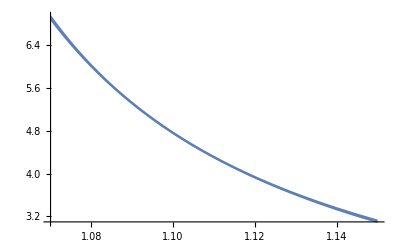

```mathematica
Lor= 1/(√((ω0^2-Ω^2)^2+(γ Ω)^2));
Plot[{a, Lor}/.{ω0->1, ω->1.1, Ω->o, γ->0.01},{o,1.07,1.15}]
```

```mathematica
Solve[D[a, Ω]==0, Ω]
```

{{Ω→(2 (ω^3+ω ω0^2))/(γ^2+4 ω^2)}}

## beyond the first Jacobian

```mathematica
J2 = J[eqs, {ddu,ddv}]
M = -Ω^2 J2 + (2 J2 ω IdentityMatrix[2] + I J1) Ω - J2 ω^2 IdentityMatrix[2] - I J1 ω + J0;
```

{{1,0},{0,1}}

```mathematica
{λs, vs} = Eigensystem[M/.η->0]//FullSimplify
```

{{ⅈ γ Ω-Ω^2+ω0^2,(2 ω-Ω) (-ⅈ γ-2 ω+Ω)+ω0^2},{{-ⅈ,1},{ⅈ,1}}}

```mathematica
δU = R.Inverse[I Ω PauliMatrix[0] + DM].Inverse[R].Inverse[J1].ξ /. η->0 //FullSimplify
a =Norm[δU] √2//FullSimplify//ComplexExpand
δx =(Re[δU[[1]]] +Im[δU[[2]]]) Cos[Ω t]-(Im[δU[[1]]] -Re[δU[[2]]])Sin[Ω t]//ComplexExpand//FullSimplify
```

{1/(2 ω^2+2 ⅈ γ Ω-4 ω Ω+2 ω0^2),ⅈ/(2 (ω^2+ⅈ γ Ω-2 ω Ω+ω0^2))}

1/(√(γ^2 Ω^2+(ω^2-2 ω Ω+ω0^2)^2))

((ω^2-2 ω Ω+ω0^2) Cos[t Ω]+γ Ω Sin[t Ω])/(ω^4-4 ω^3 Ω+γ^2 Ω^2+4 ω^2 Ω^2+2 ω (ω-2 Ω) ω0^2+ω0^4)

```mathematica
J2//MatrixForm
J1//MatrixForm
J0//MatrixForm
```

(1 | 0
0 | 1)

(γ | 2 ω
-2 ω | γ)

(-ω^2+ω0^2 | γ ω
-γ ω | -ω^2+ω0^2)